```mathematica
(*反時計まわりが正か負か，人によってことなる．
反時計回りが正のことが多いようなので，ここでもそのように決める*)
```

### 回転行列

```mathematica
Clear["Global`*"];
(*Rs[{a_,b_,c_,d_}]:=Module[{ind,s,a2,b2,c2,d2},
a2=a*a;
b2=b*b;
c2=c*c;
d2=d*d;
(*s=1/(a*a+b*b+c*c+d*d);*)
(*{{-2*s*(c2+d2),
2*s*(b*c-d*a),
2*s*(b*d+c*a)},
{2*s*(b*c+d*a),
-2*s*(b2+d2),
2*s*(c*d-b*a)},
{2*s*(b*d-c*a),
2*s*(c*d+b*a),
-2*s*(b2+c2)}}*)
s=1;
(*{{-2*s*(c2+d2),
2*s*(b*c-d*a),
2*s*(b*d+c*a)},
{2*s*(b*c+d*a),
-2*s*(b2+d2),
2*s*(c*d-b*a)},
{2*s*(b*d-c*a),
2*s*(c*d+b*a),
-2*s*(b2+c2)}}*)
(*{{a2+b2-c2-d2,2*b*c-2a*d,2b*d+2a*c},
{2b*c+2a*d,a2-b2+c2-d2,2c*d-2a*b},
{2b*d-2a*c,2c*d+2a*b,a2-b2-c2+d2}}*)
{{a2+b2-c2-d2,2*b*c+2*a*d,-2*a*c+2*b*d},
{2*b*c-2*a*d,a2-b2+c2-d2,2*a*b+2*c*d},
{2*a*c+2*b*d,-2*a*b+2*c*d,a2-b2-c2+d2}}
];*)
Rs[{a_,b_,c_,d_}]:=Module[{ind,s,a2,b2,c2,d2,div},
a2=a*a;
b2=b*b;
c2=c*c;
d2=d*d;
(*s=(a2+b2+c2+d2);*)
s=1;
{{a2+b2-c2-d2,2*b*c+2*a*d,-2*a*c+2*b*d}/s,
{2*b*c-2*a*d,a2-b2+c2-d2,2*a*b+2*c*d}/s,
{2*a*c+2*b*d,-2*a*b+2*c*d,a2-b2-c2+d2}/s}
];
Rv[{a_,b_,c_,d_}]=Inverse@Rs[{a,b,c,d}];

AxisAngleToQuaternion[{axX_,axY_,axZ_},angle_]:=Module[{n},
n=Normalize[{axX,axY,axZ}];
Return[{Cos[-angle/2],n[[1]]*Sin[-angle/2],n[[2]]*Sin[-angle/2],n[[3]]*Sin[-angle/2]}];
]
(*IDEN ={{1,0,0},{0,1,0},{0,0,1}};
S[{a_,b_,c_,d_}]:=1/Sqrt[(a*a+b*b+c*c+d*d)];
R[{a_,b_,c_,d_}]:=IDEN+R0[{a,b,c,d}]*S[{a,b,c,d}];*)
rep={a^2->a2,b^2->b2,d^2->d2,c^2->c2,
a^3->a3,b^3->b3,d^3->d3,c^3->c2,
(a2 + b2 + c2 + d2)->a2b2c2d2,
u0^2->u02,u1^2->u12,u2^2->u22,u3^2->u32,u4^2->u42,u5^2->u52,gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2->normGM2,Power->pow};

R[{a_,b_,c_,d_}]:=Rs[{a,b,c,d}];

Tmag = {{Tmag00,Tmag01,Tmag02},
{Tmag10,Tmag11,Tmag12},
{Tmag20,Tmag21,Tmag22}};

Tmag={{1,0,0},{0,1,0},{0,0,1}};

RR[{a_,b_,c_,d_}]:=Module[{zeros,r,a2,b2,c2,d2,s},
a2=a*a;
b2=b*b;
c2=c*c;
d2=d*d;
(*s=(a2+b2+c2+d2);*)
s=1;
zeros=Table[Table[0,{i,0,2,1}],{j,0,2,1}];
r=Rs[{a,b,c,d}]/s;(*ベクトルを回転する行列*)
Join[Join[r,zeros,2],Join[zeros,Dot[r,Tmag],2]]
]
```

```mathematica
(*磁場センサーのキャリブレーション*)
(*InitM= {InitMx,InitMy,InitMz}*)
{bx,by,bz}={1.22,1.32,0.62}
{Mx0,My0,Mz0}={-11.54,-12.3,-8.2}
{Mx1,My1,Mz1}={-11.8,-12.6,-4.1}
{Mx2,My2,Mz2}={-14.6,-8.1,-4.8}

InitM={Mx0,My0,Mz0}; {InitMx,InitMy,InitMz}

InvRs0=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},0/180*Pi]]
InvRs1=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},120/180*Pi]]
InvRs2=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},240/180*Pi]]


Mb[{Mx_,My_,Mz_}]:={{Mx-bx,My-by,Mz-bz,0,0,0,0,0,0},
{0,0,0,Mx-bx,My-by,Mz-bz,0,0,0},
{0,0,0,0,0,0,Mx-bx,My-by,Mz-bz}}

MatrxMb=Join[Mb[{Mx0,My0,Mz0}],
Mb[{Mx1,My1,Mz1}],
Mb[{Mx2,My2,Mz2}]]

RsInitM=Join[Dot[InvRs0,InitM],
Dot[InvRs1,InitM],
Dot[InvRs2,InitM]]

FullSimplify@Dot[Inverse[MatrxMb],RsInitM]
```

{1.22,1.32,0.62}

{-11.54,-12.3,-8.2}

{-11.8,-12.6,-4.1}

{-14.6,-8.1,-4.8}

{InitMx,InitMy,InitMz}

{{1,0,0},{0,1,0},{0,0,1}}

{{0,1,0},{0,0,1},{1,0,0}}

{{0,0,1},{1,0,0},{0,1,0}}

{{-12.76,-13.62,-8.82,0,0,0,0,0,0},{0,0,0,-12.76,-13.62,-8.82,0,0,0},{0,0,0,0,0,0,-12.76,-13.62,-8.82},{-13.02,-13.92,-4.72,0,0,0,0,0,0},{0,0,0,-13.02,-13.92,-4.72,0,0,0},{0,0,0,0,0,0,-13.02,-13.92,-4.72},{-15.82,-9.42,-5.42,0,0,0,0,0,0},{0,0,0,-15.82,-9.42,-5.42,0,0,0},{0,0,0,0,0,0,-15.82,-9.42,-5.42}}

{-11.54,-12.3,-8.2,-12.3,-8.2,-11.54,-8.2,-11.54,-12.3}

{0.0197872,0.905085,-0.117885,0.532323,-0.253073,1.01524,0.875692,0.260873,-0.740014}

```mathematica
dQdt[Q_,{w0_,w1_,w2_}]:=Module[{},
Return@{Dot[{0,-w0,-w1,-w2},Q]/2,
Dot[{w0,0,w2,-w1},Q]/2,
Dot[{w1,-w2,0,w0},Q]/2,
Dot[{w2,w1,-w0,0},Q]/2};
]
```

### 姿勢の計算の関数

```mathematica
(*満たすべき方程式*)
Q=Table[q[i],{i,0,3,1}];
{v0[0],v0[1],v0[2],v0[3],v0[4],v0[5]}={gx0,gy0,gz0,mx0,my0,mz0};(*物体の加速度を無視し，重力加速度だけがかかっている．実際は{gx0,gy0,gz0}に物体の加速度がかかっている*)
{u[0],u[1],u[2],u[3],u[4],u[5]}={Ax,Ay,Az,Mx,My,Mz};(*sensor value*)


Print["RR(q)=RR({a,b,c,d})=",RR[{a,b,c,d}]//MatrixForm]
(*関数*)

originalEq[{a_,b_,c_,d_}]=Module[{},
Table[(u[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}]
];
CForm[FullSimplify[originalEq[{a,b,c,d}]]]/.rep/.rep/.Power->pow


f[{a_,b_,c_,d_}]=Sum[(u[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}]/4(*+(1-Sqrt[a^2+b^2+c^2+d^2])*);
(*最小にする関数の微分*)
F[{a_,b_,c_,d_}]=Simplify@{
D[f[{A,b,c,d}],A]/.{A->a},
D[f[{a,B,c,d}],B]/.{B->b},
D[f[{a,b,C,d}],C]/.{C->c},
D[f[{a,b,c,dd}],dd]/.{dd->d}
};
(*最小にする関数の微分の微分*)
DF[{a_,b_,c_,d_}]=Simplify[{
D[F[{A,b,c,d}],A]/.{A->a},
D[F[{a,B,c,d}],B]/.{B->b},
D[F[{a,b,C,d}],C]/.{C->c},
D[F[{a,b,c,dd}],dd]/.{dd->d}}];

Fmod[{a_,b_,c_,d_},A_,M_]:=F[{a,b,c,d}]/.{Ax->A[[1]],Ay->A[[2]],Az->A[[3]],Mx->M[[1]],My->M[[2]],Mz->M[[3]]}
DFmod[{a_,b_,c_,d_},A_,M_]:=DF[{a,b,c,d}]/.{Ax->A[[1]],Ay->A[[2]],Az->A[[3]],Mx->M[[1]],My->M[[2]],Mz->M[[3]]}
```

RR(q)=RR({a,b,c,d})=(a^2+b^2-c^2-d^2 | 2 b c+2 a d | -2 a c+2 b d | 0 | 0 | 0
2 b c-2 a d | a^2-b^2+c^2-d^2 | 2 a b+2 c d | 0 | 0 | 0
2 a c+2 b d | -2 a b+2 c d | a^2-b^2-c^2+d^2 | 0 | 0 | 0
0 | 0 | 0 | a^2+b^2-c^2-d^2 | 2 b c+2 a d | -2 a c+2 b d
0 | 0 | 0 | 2 b c-2 a d | a^2-b^2+c^2-d^2 | 2 a b+2 c d
0 | 0 | 0 | 2 a c+2 b d | -2 a b+2 c d | a^2-b^2-c^2+d^2)

List(pow(Ax - a2*gx0 - b2*gx0 + (c2 + d2)*gx0 + a*(-2*d*gy0 + 2*c*gz0) - 2*b*(c*gy0 + d*gz0),2),
   pow(Ay + 2*a*d*gx0 - a2*gy0 + b2*gy0 - c2*gy0 + d2*gy0 - 2*c*d*gz0 - 2*b*(c*gx0 + a*gz0),2),
   pow(Az - 2*(a*c*gx0 + b*d*gx0 - a*b*gy0 + c*d*gy0) + (-a2 + b2 + c2 - d2)*gz0,2),
   pow(Mx - a2*mx0 - b2*mx0 + (c2 + d2)*mx0 + a*(-2*d*my0 + 2*c*mz0) - 2*b*(c*my0 + d*mz0),2),
   pow(2*a*d*mx0 + My - a2*my0 + b2*my0 - c2*my0 + d2*my0 - 2*c*d*mz0 - 2*b*(c*mx0 + a*mz0),2),
   pow(-2*(a*c*mx0 + b*d*mx0 - a*b*my0 + c*d*my0) + Mz + (-a2 + b2 + c2 - d2)*mz0,2))

```mathematica
yaw[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*d+b*c)/(1-2*(c*c+d*d))]
roll[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*b+c*d)/(1-2*(b*b+c*c))]
pitch[{a_,b_,c_,d_}]:=N@ArcSin[2*(a*c-b*d)]
```

### 姿勢の計算１：物体の加速度を無視し，重力加速度だけがかかっているとして，物体の姿勢を計測する方法

```mathematica
(*上で設定した，初期のgとmを回転させることで，センサーの値を模擬*)
(****************************************************)
{axis,dθ}={{0,0,1},70/180.*Pi};
q=AxisAngleToQuaternion[axis,dθ];(*この回転を表すクォータニオン*)
A=Dot[Rs[q],{gx0,gy0,gz0}];(*加速度 g^*)
M=Dot[Rs[q],{mx0,my0,mz0}](*磁場 m^*)
```

{0.+0.34202 mx0-0.939693 my0,0.+0.939693 mx0+0.34202 my0,0.+1. mz0}

```mathematica
{a,b,c,d}=getQ[A,M]
```

Set::shape: {a,b,c,d}とgetQ[{0.+0.34202 gx0-0.939693 gy0,0.+0.939693 gx0+0.34202 gy0,0.+1. gz0},{0.+0.34202 mx0-0.939693 my0,0.+0.939693 mx0+0.34202 my0,0.+1. mz0}]のリストは型が違います．

getQ[{0.+0.34202 gx0-0.939693 gy0,0.+0.939693 gx0+0.34202 gy0,0.+1. gz0},{0.+0.34202 mx0-0.939693 my0,0.+0.939693 mx0+0.34202 my0,0.+1. mz0}]

```mathematica
{a,b,c,d}=getQ[A,M];
Norm[{a,b,c,d}]
(*{a,b,c,d}=Normalize[{a,b,c,d}]*)
(*l=A*)
(*solution={Cos[θ/2.],l[[1]]*Sin[θhorion/2],l[[2]]*Sin[θhorion/2.],l[[3]]*Sin[θhorion/2.]}*)
Print["{Y,P,R}=",{yaw[{a,b,c,d}],roll[{a,b,c,d}],pitch[{a,b,c,d}](*,2ArcTan[Norm[{b,c,d}]/a]*)}/Pi*180]
```

Set::shape: {a,b,c,d}とgetQ[{0.+0.34202 gx0-0.939693 gy0,0.+0.939693 gx0+0.34202 gy0,0.+1. gz0},{0.+0.34202 mx0-0.939693 my0,0.+0.939693 mx0+0.34202 my0,0.+1. mz0}]のリストは型が違います．

√(Abs[a]^2+Abs[b]^2+Abs[c]^2+Abs[d]^2)

{Y,P,R}={(180 ArcTan[(2. (b c+a d))/(1.-2. (c^2+d^2))])/π,(180 ArcTan[(2. (a b+c d))/(1.-2. (b^2+c^2))])/π,(180 ArcSin[2. (a c-1. b d)])/π}

### チェック

```mathematica
(*Clear[a,b,c,d]
Print["空間を回転させる回転行列"]
Print[CForm[Rs[{a,b,c,d}]/.rep]]
Print["空間を固定しベクトルを回転させる回転行列"]
Print[CForm[Transpose[Rs[{a,b,c,d}]/.rep]]]
N@R[Normalize@{4,1,2,3}]*)
```

### 姿勢の計算

```mathematica
(*.08加速度をいっぺんに計算する*)
```

```mathematica
(*データの読み込み*)
```

```mathematica
imported =Import[FileNameJoin["/Users/tomoaki/Dropbox/markdown/python_shared/example_AHRS/dataAHRS.json"]];
Column@imported[[1]](*例*)
rowGyros=ParallelTable[("mag"/.#5)&@@imported[[i]],{i,1,Length[imported]}];
```

period→0.001
gyro→{1.41985,21.0076,0.145038}
accel→{-0.81665,0.0810547,-0.48169}
dt→0.013147
mag→{-3.48419,3.75336,2.94586}
time_ns→286383995000

```mathematica
{minmaxX,minmaxY,minmaxZ}=CoordinateBounds[rowGyros];
magCenterX=Mean[minmaxX]
magCenterY=Mean[minmaxY]
magCenterZ=Mean[minmaxZ]
magCenterXYZ={magCenterX,magCenterY,magCenterZ};

(*初期姿勢の静止姿勢で観測される重力加速度と磁場を設定．これはfusionの初期に一つ決める値で，DFやFに組み込まれる*)
magBias={-2.044069644509259,3.296398226566499,2.029526850118487}-magCenterXYZ;gyroBias={-0.454917765991497,-0.12121859207787493,-0.09516749018618002};
accelBias={0.014670909915040676,0.11165143283325697,-1.0097354621661374};
(****************************************************)
(*θ=-54/180*Pi;
{gx0,gy0,gz0}={0,0,-1};(*g0*)
{mx0,my0,mz0}={Cos[θ],0,Sin[θ]};(*m0*)
*)

{gx0,gy0,gz0}=accelBias;(*g0*)
{mx0,my0,mz0}=magBias;(*m0*)
(****************************************************)
{a,b,c,d}={RandomReal[],RandomReal[],RandomReal[],RandomReal[]};
getQuaternion[A0_,M0_,Q_]:=Module[{data,abcd,dq,DQ,Ax,Ay,Az,Mx,My,Mz,a,b,c,d,M,A},
M=Normalize@M0;
A=Normalize@A0;
{a,b,c,d}=Normalize@Q;
dq={1,0,0,0};
Do[
dq=(Dot[Inverse[DFmod[{a,b,c,d},A,M]],Fmod[{a,b,c,d},A,M]]);
{a,b,c,d}-=dq;
{a,b,c,d}=Normalize[{a,b,c,d}];
If[Abs[dq]<10^-8,Break;];
,{i,0,10,1}];
Return[{a,b,c,d}];
]
```

-1.82434

1.75705

4.09729

### シミュレーション

```mathematica
P={};
W={};
A={};
Abody={};
AbodyAccum={};
AbodyByApproxQ={};
AbodyByCombinedQ={};
AXRawer={};
AYRawer={};
AZRawer={};

AXRaw={};
AYRaw={};
AZRaw={};

dT={};
T={};
M={};
MX={};
MY={};
MZ={};
Q={};
q={RandomReal[],RandomReal[],RandomReal[],RandomReal[]};
starttime=("time_ns"/.#6)*10^-9&@@imported[[1]]

w=a=aRawer={0,0,0};
t=0;
abody=abodyAccum=abodyByApproxQ=abodyByCombinedQ={0,0,0};
m={0,0,0};
α=.5;
αraw=.9;
β=.5;
γ=.9;
(*シミュレーション*)
Do[
data=imported[[i]];
{p,dt,rowgyro,rowaccel,rowmag,timens}={"period","dt","gyro","accel","mag","time_ns"}/.data;
lastw=w;
w=γ*(rowgyro-gyroBias)+(1-γ)*w;
a=α*(rowaccel)+(1-α)*a;
aRawer=αraw*(rowaccel)+(1-αraw)*aRawer;
m=β*(rowmag-magCenterXYZ)+(1-β)*m;
remotedt=timens*10^-9-starttime-t;
t=timens*10^-9-starttime;

(*Print[p,w,a,dt,m,t,remotedt,dQdt[q,w]];*)
approxq=Normalize[(q+remotedt*dQdt[q,w])];

q=Normalize[Quiet@getQuaternion[a,m,q]];

abody=(aRawer-Dot[Rs[q],{0,0,-1}]);

abodyAccum=0.8*abodyAccum+0.2*abody;

abodyByApproxQ=(aRawer-Dot[Rs[approxq],{0,0,-1}]);

c=0.5;
CombinedQ=Normalize[((1-c)*approxq+c*q)];
abodyByCombinedQ=(aRawer-Dot[Rs[CombinedQ],{0,0,-1}]);

(*q=CombinedQ;*)

AppendTo[P,p];
AppendTo[W,w];
AppendTo[A,a];
AppendTo[Abody,abody];
AppendTo[AbodyAccum,abodyAccum];
AppendTo[AbodyByApproxQ,abodyByApproxQ];
AppendTo[AbodyByCombinedQ,abodyByCombinedQ];
AppendTo[AXRawer,aRawer[[1]]];
AppendTo[AYRawer,aRawer[[2]]];
AppendTo[AZRawer,aRawer[[3]]];
AppendTo[AXRaw,rowaccel[[1]]];
AppendTo[AYRaw,rowaccel[[2]]];
AppendTo[AZRaw,rowaccel[[3]]];
AppendTo[M,m];
AppendTo[MX,m[[1]]];
AppendTo[MY,m[[2]]];
AppendTo[MZ,m[[3]]];
AppendTo[T,t];
AppendTo[Q,q];
,{i,1,Length[imported]}]
```

57276799/200000

```mathematica
ListPointPlot3D[Table[{T[[i]],M[[i]]},{i,1,Length[T]}],BoxRatios->{1, 1, 1},PlotLabel->"磁気データ"]
ListPointPlot3D[Table[{T[[i]],A[[i]]},{i,1,Length[T]}],BoxRatios->{1, 1, 1},PlotLabel->"加速度データ"]
```

-Graphics3D-

-Graphics3D-

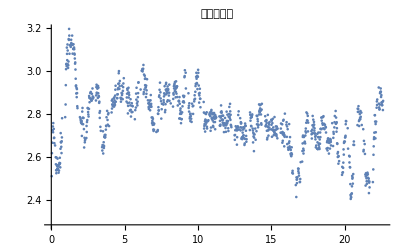

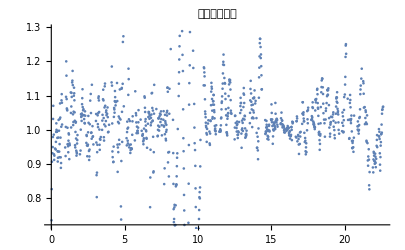

```mathematica
ListPlot[Table[{T[[i]],Norm@M[[i]]},{i,1,Length[T]}],PlotLabel->"磁気データ"]
ListPlot[Table[{T[[i]],Norm@A[[i]]},{i,1,Length[T]}],PlotLabel->"加速度データ"]
```

```mathematica
Rs[{a0_,b0_,c0_,d0_}]:=Module[{ind,s,a2,b2,c2,d2,div,a,b,c,d},
{a,b,c,d}=Normalize@{a0,b0,c0,d0};
a2=a*a;
b2=b*b;
c2=c*c;
d2=d*d;
{{a2+b2-c2-d2,2*b*c+2*a*d,-2*a*c+2*b*d},
{2*b*c-2*a*d,a2-b2+c2-d2,2*a*b+2*c*d},
{2*a*c+2*b*d,-2*a*b+2*c*d,a2-b2-c2+d2}}
];

LowPass[AXRawer_,α_]:=Module[{Ret},
Ret=AXRawer;
Do[
a=Abs[AXRawer[[i+1]]/Ret[[i]]-1];
If[a>.1,
Ret[[i+1]]=α/10*AXRawer[[i+1]]+(α/10-1)*Ret[[i]];,
Ret[[i+1]]=α*AXRawer[[i+1]]+(α-1)*Ret[[i]];
];

,{i,1,Length[Ret]-1}];
Return[Ret];
];
```

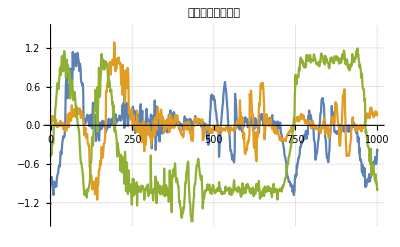

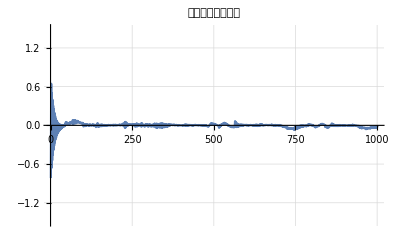

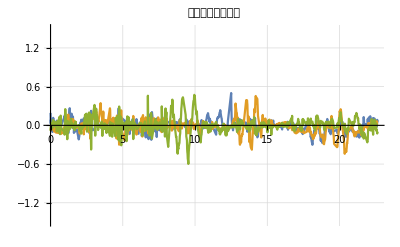

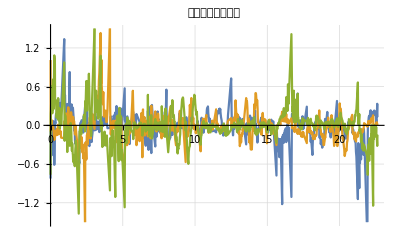

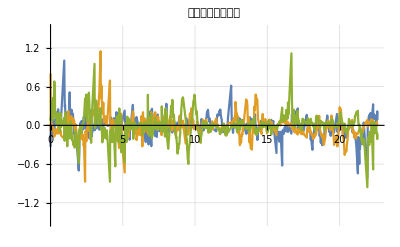

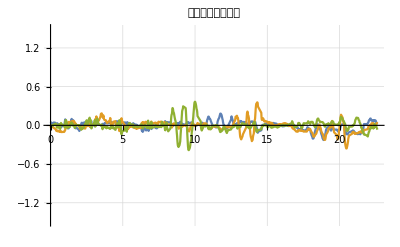

```mathematica
ListPlot[{AXRaw,AYRaw,AZRaw},Joined->True,PlotLabel->"加速度成分データ",PlotRange->{Automatic,{-1.5,1.5}},GridLines->Automatic]
ListPlot[Table[LowPass[AXRaw,α],{α,1.,1.,0.3}],Joined->True,PlotLabel->"加速度成分データ",PlotRange->{Automatic,{-1.5,1.5}},GridLines->Automatic]

accelXYZ=Abody;
accelX=Table[{T[[i]],accelXYZ[[i]][[1]]},{i,1,Length[Q]}];
accelY=Table[{T[[i]],accelXYZ[[i]][[2]]},{i,1,Length[Q]}];
accelZ=Table[{T[[i]],accelXYZ[[i]][[3]]},{i,1,Length[Q]}];
ListPlot[{accelX,accelY,accelZ},Joined->True,PlotLabel->"加速度成分データ",PlotRange->{Automatic,{-1.5,1.5}},GridLines->Automatic]

accelXYZ=AbodyByApproxQ;
accelX=Table[{T[[i]],accelXYZ[[i]][[1]]},{i,1,Length[Q]}];
accelY=Table[{T[[i]],accelXYZ[[i]][[2]]},{i,1,Length[Q]}];
accelZ=Table[{T[[i]],accelXYZ[[i]][[3]]},{i,1,Length[Q]}];
ListPlot[{accelX,accelY,accelZ},Joined->True,PlotLabel->"加速度成分データ",PlotRange->{Automatic,{-1.5,1.5}},GridLines->Automatic]

accelXYZ=AbodyByCombinedQ;
accelX=Table[{T[[i]],accelXYZ[[i]][[1]]},{i,1,Length[Q]}];
accelY=Table[{T[[i]],accelXYZ[[i]][[2]]},{i,1,Length[Q]}];
accelZ=Table[{T[[i]],accelXYZ[[i]][[3]]},{i,1,Length[Q]}];
ListPlot[{accelX,accelY,accelZ},Joined->True,PlotLabel->"加速度成分データ",PlotRange->{Automatic,{-1.5,1.5}},GridLines->Automatic]

accelXYZ=AbodyAccum;
accelX=Table[{T[[i]],accelXYZ[[i]][[1]]},{i,1,Length[Q]}];
accelY=Table[{T[[i]],accelXYZ[[i]][[2]]},{i,1,Length[Q]}];
accelZ=Table[{T[[i]],accelXYZ[[i]][[3]]},{i,1,Length[Q]}];
ListPlot[{accelX,accelY,accelZ},Joined->True,PlotLabel->"加速度成分データ",PlotRange->{Automatic,{-1.5,1.5}},GridLines->Automatic]
```

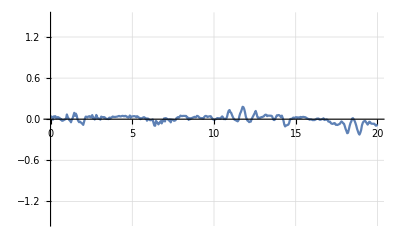

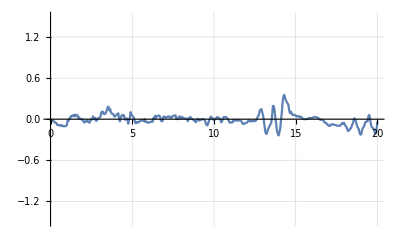

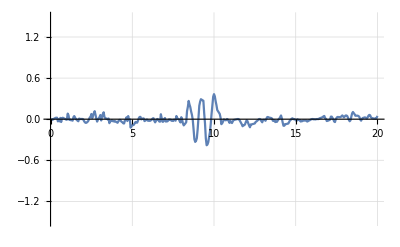

```mathematica
intpX=Interpolation[Table[{T[[i]],AbodyAccum[[i]][[1]]},{i,1,Length[Q]}],InterpolationOrder->1];
ListPlot[ParallelTable[{x,intpX[x]},{x,0,20,.05}],Joined->True,PlotRange->{Automatic,{-1.5,1.5}},GridLines->Automatic]
intpY=Interpolation[Table[{T[[i]],AbodyAccum[[i]][[2]]},{i,1,Length[Q]}],InterpolationOrder->1];
ListPlot[ParallelTable[{x,intpY[x]},{x,0,20,.05}],Joined->True,PlotRange->{Automatic,{-1.5,1.5}},GridLines->Automatic]
intpZ=Interpolation[Table[{T[[i]],AbodyAccum[[i]][[3]]},{i,1,Length[Q]}],InterpolationOrder->1];
ListPlot[ParallelTable[{x,intpZ[x]},{x,0,20,.05}],Joined->True,PlotRange->{Automatic,{-1.5,1.5}},GridLines->Automatic]
```

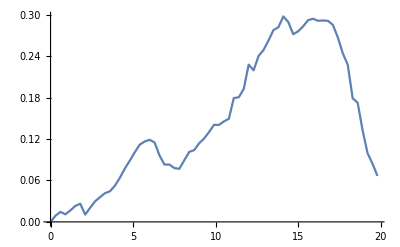

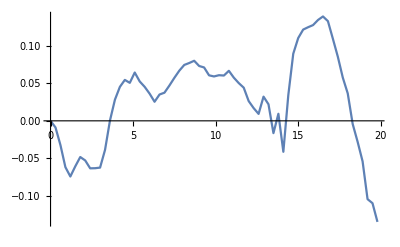

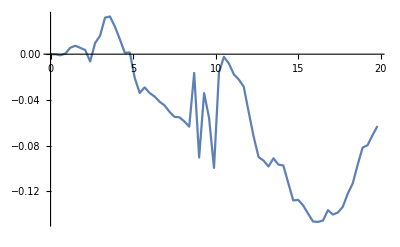

```mathematica
ListPlot[ParallelTable[{end,NIntegrate[intpX[x],{x,0,end}]},{end,0,20,.3}],Joined->True]
ListPlot[ParallelTable[{end,NIntegrate[intpY[x],{x,0,end}]},{end,0,20,.3}],Joined->True]
ListPlot[ParallelTable[{end,NIntegrate[intpZ[x],{x,0,end}]},{end,0,20,.3}],Joined->True]
```

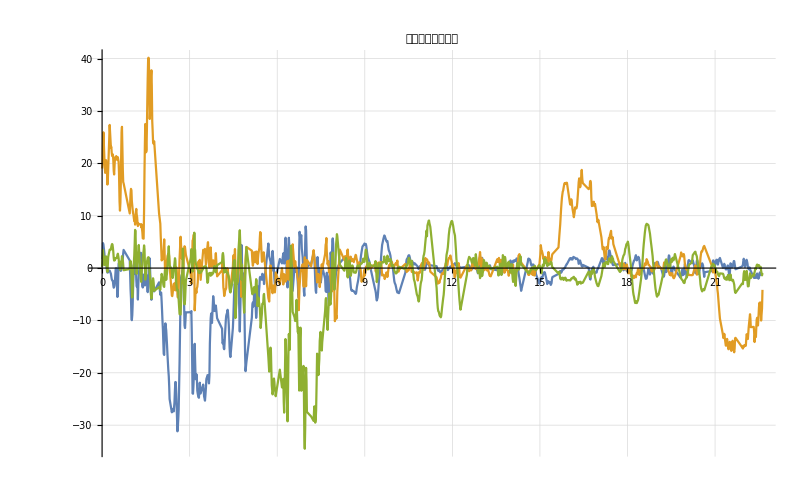

```mathematica
accelX=Table[{T[[i]],W[[i]][[1]]},{i,1,Length[Q]}];
accelY=Table[{T[[i]],W[[i]][[2]]},{i,1,Length[Q]}];
accelZ=Table[{T[[i]],W[[i]][[3]]},{i,1,Length[Q]}];
ListPlot[{accelX,accelY,accelZ},Joined->True,PlotLabel->"加速度成分データ",PlotRange->All,GridLines->Automatic]
```